# Heavy neutrino decays

```mathematica
<<FeynCalc`
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/matheus/Repos/SolarNus/mathematica

```mathematica
dm[mu_]:=GA[mu]
dm[5]:=DiracMatrix[5]
ds[p_]:=DiracSlash[p]
mt[mu_,nu_]:=MetricTensor[mu,nu]
fv[p_,mu_]:=FourVector[p,mu]
epsilon[a_,b_,c_,d_]:=LeviCivita[a,b,c,d]
id[n_]:=IdentityMatrix[n]
sp[p_,q_]:=ScalarProduct[p,q]
li[mu_]:=LorentzIndex[mu]
prop[p_,m_]:=ds[p]+m
PR=dm[6];
PL=dm[7];
dσ[μ_,ν_]:=I/2(dm[μ].dm[ν]-dm[ν].dm[μ]);
SetOptions[{DiracMatrix, DiracSlash,LeviCivita, FourVector, MetricTensor, SetMandelstam, OneLoop, ScalarProduct},Dimension->4];
```

## Amplitudes

## ν_h (k1) --> v_i (k2) l_β-(k3) l_α+(k4)

```mathematica
MajAmp=( (-MT[μ,ν])/( MZBOSON^2)SpinorUBar[k2,m2].dm[ν].PL.SpinorV[k3,m3])
```

```mathematica
MajAmpC =((-MT[μ,ν])/(sp[k2-k1,k2-k1] - MZBOSON^2)ComplexConjugate[SpinorUBar[k2,m2].(Cih dm[μ].PL ) . ((1+ h dm[5].ds[s])/2).SpinorU[k1,m1]]ComplexConjugate[  SpinorUBar[k3,m3].dm[ν].(Cv- Ca dm[5]).SpinorV[k4,m4]] +   (-MT[μ,ν])/(sp[k2-k1,k2-k1] - MZPRIME^2)ComplexConjugate[SpinorUBar[k2,m2].(Dih dm[μ].PL).((1+ h dm[5].ds[s])/2).SpinorU[k1,m1]]ComplexConjugate[  SpinorUBar[k3,m3].dm[ν].(Dv- Da dm[5]).SpinorV[k4,m4]])*NCflag+(gweak^2/2((-MT[μ,ν])/(sp[k1-k3,k1-k3] - MW^2))(ComplexConjugate[SpinorUBar[k2,m2].dm[μ].PL.((1+ h dm[5].ds[s])/2).SpinorU[k1,m1]]ComplexConjugate[ SpinorUBar[k3,m3].dm[ν].PL.SpinorV[k4,m4]])CCflag1 ) /.{μ-> μ2,ν-> ν2};
```

```mathematica
MajAmpAVE=( (-MT[μ,ν])/(sp[k2-k1,k2-k1] - MZBOSON^2)SpinorUBar[k2,m2].(Cih dm[μ].PL ).SpinorU[k1,m1] SpinorUBar[k3,m3].dm[ν].(Cv- Ca dm[5]).SpinorV[k4,m4] +  (-MT[μ,ν])/(sp[k2-k1,k2-k1] - MZPRIME^2)SpinorUBar[k2,m2].(Dih dm[μ].PL).SpinorU[k1,m1] SpinorUBar[k3,m3].dm[ν].(Dv- Da dm[5]).SpinorV[k4,m4]) *NCflag+gweak^2/2((-MT[μ,ν])/(sp[k1-k3,k1-k3] - MW^2))(SpinorUBar[k2,m2].dm[μ].PL.SpinorU[k1,m1]SpinorUBar[k3,m3].dm[ν].PL.SpinorV[k4,m4])*CCflag1;
```

```mathematica
MajAmpCAVE =((-MT[μ,ν])/(sp[k2-k1,k2-k1] - MZBOSON^2)ComplexConjugate[SpinorUBar[k2,m2].(Cih dm[μ].PL) .SpinorU[k1,m1]]ComplexConjugate[  SpinorUBar[k3,m3].dm[ν].(Cv- Ca dm[5]).SpinorV[k4,m4]] +   (-MT[μ,ν])/(sp[k2-k1,k2-k1] - MZPRIME^2)ComplexConjugate[SpinorUBar[k2,m2].(Dih dm[μ].PL).SpinorU[k1,m1]]ComplexConjugate[  SpinorUBar[k3,m3].dm[ν].(Dv- Da dm[5]).SpinorV[k4,m4]])*NCflag+gweak^2/2((-MT[μ,ν])/(sp[k1-k3,k1-k3] - MW^2))(ComplexConjugate[SpinorUBar[k2,m2].dm[μ].PL.SpinorU[k1,m1]]ComplexConjugate[ SpinorUBar[k3,m3].dm[ν].PL.SpinorV[k4,m4]])CCflag1  /.{μ-> μ2,ν-> ν2};
```

## Spin sums and Trace

```mathematica
MajAmpSQR = FermionSpinSum[MajAmpC MajAmp]//Simplify;
```

```mathematica
TracedMajAmpSQR = MajAmpSQR/.{DiracTrace-> Tr}/.{k4-> k1 -k2-k3}//Contract
```

-(CCflag1^2 h m1 (OverBar[k2]·OverBar[k3]) (OverBar[k1]·s̄-OverBar[k2]·s̄-OverBar[k3]·s̄) gweak^4)/((MW^2-OverBar[k1]^2+2 (OverBar[k1]·OverBar[k3])-OverBar[k3]^2)^2)+324+(4 Dih^2 Dv^2 m3 m4 NCflag^2 (OverBar[k1]·OverBar[k2]))/((MZPRIME^2-OverBar[k1]^2+2 (OverBar[k1]·OverBar[k2])-OverBar[k2]^2)^2)
 |  |  |  |

```mathematica
MajAmpSQRAVERAGED = FermionSpinSum[MajAmpCAVE MajAmpAVE]//Simplify;
```

```mathematica
TracedMajAmpSQRAVERAGED = MajAmpSQRAVERAGED/.{DiracTrace-> Tr}/.{k4-> k1 -k2-k3}//Contract;
```

# Kinematics

## Substitute kinematical variables

```mathematica
Lambda[a_,b_, c_] := (a-b-c)-4b c
subP = {Pair[Momentum[k1],Momentum[k1]]-> m1^2,
Pair[Momentum[k2],Momentum[k2]]->m2^2,
Pair[Momentum[k3],Momentum[k3]]->m3^2,
Pair[Momentum[k4],Momentum[k4]]->m4^2,
Pair[Momentum[k1],Momentum[k2]]->(-m34sqr+m1^2+m2^2)/2,
Pair[Momentum[k1],Momentum[k3]]->-1/2(m24sqr - m1^2-m3^2),
Pair[Momentum[k1],Momentum[k4]]->(-m23sqr+m1^2+m4^2)/2,
Pair[Momentum[k2],Momentum[k3]]->(m23sqr-m2^2-m3^2)/2,
Pair[Momentum[k2],Momentum[k4]]->(m24sqr-m4^2-m2^2)/2,
Pair[Momentum[k3],Momentum[k4]]->(m34sqr-m4^2-m3^2)/2,
Pair[Momentum[s],Momentum[s]]-> -1,
Pair[Momentum[k1],Momentum[s]]-> 0,
Pair[Momentum[k2],Momentum[s]]-> k3CM*c3+k4CM*c4,
Pair[Momentum[k3],Momentum[s]]-> -k3CM *c3,
Pair[Momentum[k4],Momentum[s]]-> -k4CM*c4};

subPexpressions={
k4CM->m1/2 √Lambda[1,m23sqr/m1^2,m4^2/m1^2],k3CM->m1/2 √Lambda[1,m24sqr/m1^2,m3^2/m1^2],
k2CM->m1/2 √Lambda[1,m34sqr/m1^2,m2^2/m1^2]};

subMassNorm ={m1-> 1  m1,m2-> x2 m1, m3-> x3 m1, m4 -> x4 m1, m24sqr-> x24 m1^2,m23sqr-> x23 m1^2, m34sqr-> x34 m1^2,MW-> xWBOSON m1,MZBOSON-> xZBOSON m1, MZPRIME-> xZPRIME m1};
```

## phase space

```mathematica
PS3 = m1^2/(32 (2 π)^5);
FluxFactor=1/(2 m1);
SpinAverage = 1/2;
```

### Substitute in the special cases

```mathematica
subFULL={CihC-> Cih, DihC-> Dih};
subNConly={Dv-> 0, Da-> 0,Dih-> 0,DihC-> 0,Cih-> Subscript[U, μ4] gweak/(2Cos[W]),CihC-> Subscript[U, μ4] gweak/(2Cos[W]),Ca-> -gweak/(4Cos[W]),Cv-> gweak/(2Cos[W])(-1/2+2 Sin[W]^2),CCflag1-> 0,CCflag2-> 0, NCflag-> (MZBOSON^2-m34sqr)/MZBOSON^2};
subNCplusCC={Dv-> 0, Da-> 0,Dih-> 0,DihC-> 0,Cih-> Subscript[U, μ4] gweak/(2Cos[W]),CihC-> Subscript[U, μ4] gweak/(2Cos[W]),Ca-> -gweak/(4Cos[W]),Cv-> gweak/(2Cos[W])(-1/2+2 Sin[W]^2),CCflag1-> (Subscript[U, μ4](MW^2-m24sqr))/(MZBOSON^2 Cos[W]^2),CCflag2-> -Subscript[U, μ4](MW^2+m24sqr+m34sqr-m1^2)/(MZBOSON^2 Cos[W]^2), NCflag-> (MZBOSON^2-m34sqr)/MZBOSON^2};
subCConly={Dv-> 0, Da-> 0,Cih-> Subscript[U, μ4] ,CCflag1-> (Subscript[U, μ4](MW^2-m24sqr))/(MZBOSON^2 Cos[W]^2),CCflag2->-Subscript[U, μ4](MW^2+m24sqr+m34sqr-m1^2)/(MZBOSON^2 Cos[W]^2), NCflag-> 0};
subMassless={x2-> 0, x3->0,x4-> 0};
subGf={gweak-> √((8 Gf MW^2)/(√2))};
subINTEGRATION={m34sqr-> m1^2+m2^2+m3^2+m4^2-m24sqr-m23sqr };
```

### Massless integrand

```mathematica
Sim4TracedAmpSQRCC = TracedMajAmpSQR/.subP/.subCConly/.subGf/.subPexpressions/.subINTEGRATION/.subMassNorm/.subMassless/.{h^2-> 1}//FullSimplify
Sim4TracedAmpSQRNC = TracedMajAmpSQR/.subP/.subNConly/.{gweak->√(1/(√2)8 Gf MZBOSON^2 Cos[W]^2) }/.subPexpressions/.subINTEGRATION/.subMassNorm/.subMassless/.{h^2-> 1}//Simplify
Sim4TracedAmpSQRNCplusCC = TracedMajAmpSQR/.subP/.subNCplusCC/.{gweak->√(1/(√2)8 Gf MZBOSON^2 Cos[W]^2) }/.subPexpressions/.subINTEGRATION/.subMassNorm/.subMassless/.{h^2-> 1}//Simplify
```

(16 Gf^2 m1^4 x23 xWBOSON^4 U_μ4^2 (c4 h √(1-x23)-x23+1) sec^4((4 Enu M-Q2)/M^2))/xZBOSON^4

-2 Gf^2 m1^4 U_μ4^2 (cos((16 Enu M-4 Q2)/M^2) (x24 (-c3 h √(1-x24)+x24-1)-x23 (c4 h √(1-x23)+1)+x23^2)-4 x24 (-c3 h √(1-x24)+x24-1) cos((8 Enu M-2 Q2)/M^2)-3 c3 h √(1-x24) x24-c4 h √(1-x23) x23+x23^2-x23+3 x24^2-3 x24)

-2 Gf^2 m1^4 U_μ4^2 (cos((16 Enu M-4 Q2)/M^2) (x24 (-c3 h √(1-x24)+x24-1)-x23 (c4 h √(1-x23)+1)+x23^2)+4 cos((8 Enu M-2 Q2)/M^2) (x24 (c3 h √(1-x24)-x24+1)+2 x23 (c4 h √(1-x23)+1)-2 x23^2)+3 x24 (-c3 h √(1-x24)+x24-1)-9 x23 (c4 h √(1-x23)+1)+9 x23^2)

```mathematica
Integrate[Integrate[Integrate[((Sim4TracedAmpSQRCC/.h-> 1) + (Sim4TracedAmpSQRCC/.h-> -1) )* PS3*FluxFactor*SpinAverage*4 π^2,{c3,-1,1}],{x23,0,1-x24},Assumptions->{x24>0}],{x24,0,1},Assumptions->{x24>0}]/.{xWBOSON-> MZBOSON (√(1-SinW^2))/m1,xZBOSON-> MZBOSON/m1}/.{W-> ArcSin[SinW]}//Simplify
Integrate[Integrate[Integrate[((Sim4TracedAmpSQRNC/.h-> 1) + (Sim4TracedAmpSQRNC/.h-> -1) ) * PS3*FluxFactor*SpinAverage*4 π^2/.h-> 0,{c3,-1,1}],{x23,0,1-x24},Assumptions->{1>x24>0}],{x24,0,1},Assumptions->{1>x24>0}]/.{W-> ArcSin[SinW]}//Simplify
Integrate[Integrate[Integrate[((Sim4TracedAmpSQRNCplusCC/.h-> 1) + (Sim4TracedAmpSQRNCplusCC/.h-> -1) ) * PS3*FluxFactor*SpinAverage*4 π^2/.h-> 0,{c3,-1,1}],{x23,0,1-x24},Assumptions->{1>x24>0}],{x24,0,1},Assumptions->{1>x24>0}]/.{W-> ArcSin[SinW]}//Simplify
```

(Gf^2 m1^5 (SinW^2-1)^2 U_μ4^2 sec^4((4 Enu M-Q2)/M^2))/(192 π^3)

(Gf^2 m1^5 U_μ4^2 (cos((16 Enu M-4 Q2)/M^2)-2 cos((8 Enu M-2 Q2)/M^2)+2))/(768 π^3)

(Gf^2 m1^5 U_μ4^2 (cos((16 Enu M-4 Q2)/M^2)-6 cos((8 Enu M-2 Q2)/M^2)+6))/(768 π^3)

### BSM only

```mathematica
subMasslessLeptons={};
```

```mathematica
subZPRIME={Dv-> gweak χ Sin[W]Cos[W], Da-> 0,Dih-> Subscript[U, D4] gprime,DihC-> Subscript[U, D4] gprime,Cih->0,CihC-> 0,Ca-> 0,Cv-> 0,CCflag1-> 0,CCflag2-> 0, NCflag-> (MZPRIME^2-m34sqr)/MZPRIME^2};
```

```mathematica
simZprime = TracedMajAmpSQR/.subP/.subZPRIME/.subPexpressions/.subINTEGRATION/.subMassNorm/.subMasslessLeptons//FullSimplify
```

1/(4 xZPRIME^4)gprime^2 gweak^2 χ^2 U_D4^2 sin^2((8 Enu M-2 Q2)/M^2) (x2^2 (-2 c3 h √(-(4 x24+1) x3^2-x24+1)-2 c4 h √(-(4 x23+1) x4^2-x23+1)+(h^2+1) (x23+x24-x3^2-x4^2-2))+2 h (c3 √(-(4 x24+1) x3^2-x24+1) (x24-x4 (2 x3+x4))+c4 √(-(4 x23+1) x4^2-x23+1) (x23-x3 (x3+2 x4)))+h^2 (-x23^2+x23 ((x3+x4)^2+1)-x24^2+x24 (x3+x4)^2+x24-x4 (2 x3 (x3^2+x3 x4+x4^2)+x4)-x3^2)-x23^2+x4^2 (x23+x24-2 x3^2-1)+2 x3 x4 (x23+x24-x3^2)+x23 x3^2+x23-x24^2+x24 x3^2+x24-x3^2-2 x3 x4^3)

### symmetric over 3 and 4?

```mathematica
simZprime-(simZprime/.{x3-> x4,x4-> x3})//Simplify
```

-1/(2 xZPRIME^4)gprime^2 gweak^2 h χ^2 U_D4^2 sin^2((8 Enu M-2 Q2)/M^2) (c3 (x2^2 (√(-4 x24 x3^2-x24-x3^2+1)-√(-4 x24 x4^2-x24-x4^2+1))+x4^2 √(-4 x24 x3^2-x24-x3^2+1)-x3^2 √(-4 x24 x4^2-x24-x4^2+1)+2 x3 x4 √(-4 x24 x3^2-x24-x3^2+1)-x24 √(-4 x24 x3^2-x24-x3^2+1)-2 x3 x4 √(-4 x24 x4^2-x24-x4^2+1)+x24 √(-4 x24 x4^2-x24-x4^2+1))+c4 (x2^2 (√(-4 x23 x4^2-x23-x4^2+1)-√(-4 x23 x3^2-x23-x3^2+1))-x4^2 √(-4 x23 x3^2-x23-x3^2+1)+x3^2 √(-4 x23 x4^2-x23-x4^2+1)-2 x3 x4 √(-4 x23 x3^2-x23-x3^2+1)+x23 √(-4 x23 x3^2-x23-x3^2+1)+2 x3 x4 √(-4 x23 x4^2-x23-x4^2+1)-x23 √(-4 x23 x4^2-x23-x4^2+1)))

```mathematica
Integrate[Integrate[Integrate[((simZprime/.h-> 1) + (simZprime/.h-> -1) ) * PS3*FluxFactor*SpinAverage*4 π^2/.h-> 0,{c3,-1,1}],{x23,x2^2/x24,x2^2+(1-x24)},Assumptions->{1>x24>x2^2,x2> 0}],{x24,x2^2,1},Assumptions->{1>x24>x2^2,x2> 0}]/.{gweak-> e/Sin[W],xZPRIME-> MZPRIME/m1}//Simplify
```

-1/(768 π^3 MZPRIME^4)e^2 gprime^2 m1^5 χ^2 U_D4^2 cos^2((4 Enu M-Q2)/M^2) (12 x2^2 log(x2) (x2^2 (x3^2+x4^2+2)+2 x3^3 x4+x3^2 (2 x4^2+1)+2 x3 x4^3+x4^2)+(x2^2-1) (x2^6-x2^4 (x3^2-4 x3 x4+x4^2+7)-x2^2 (6 x3^3 x4+2 x3^2 (3 x4^2+5)+x3 (6 x4^3+8 x4)+10 x4^2+7)-6 x3^3 x4-x3^2 (6 x4^2+1)+x3 (4 x4-6 x4^3)-x4^2+1))

```mathematica
F[x2_]:=-Collect[x2^8+2 x2^7-8 x2^6+18 x2^5-18 x2^3+8 x2^2-24 (x2^2-x2+1) x2^3 log(x2)-2 x2-1,{x2}]//FullSimplify
```

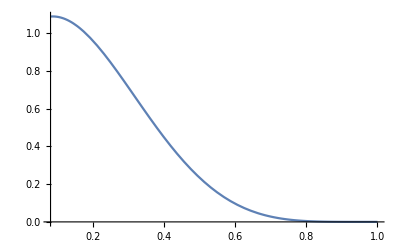

```mathematica
Plot[F[x],{x,0.08,1}]
```

```mathematica
G=F[x]/.{x-> 1-μ}//FullSimplify
```

-(μ-2) μ (μ (μ (μ (μ ((μ-8) μ+18)-32)+46)-36)+12)-24 ((μ-1) μ+1) (μ-1)^3 log(1-μ)

```mathematica
Series[G,{μ,0,8}]
```

(96 μ^5)/5-(144 μ^6)/5+(384 μ^7)/35-(24 μ^8)/35+O(μ^9)

```mathematica
Limit[x^2 Log[1/x],{x-> 0}]
```

0

### Atre&Pascoli rates

```mathematica
gl = -1/2+Sin[W]^2;gr = Sin[W]^2;
2*(Gf^2 m1^5 Subscript[U, μ4]^2)/(192 π^3)//FullSimplify
((Gf^2 m1^5 Subscript[U, μ4]^2)/(96 π^3))( gl^2+gr^2+(1+2gl))/.{W-> ArcSin[SinW]}//Simplify
```

(Gf^2 m1^5 U_μ4^2)/(96 π^3)

(Gf^2 m1^5 (8 SinW^4+4 SinW^2+1) U_μ4^2)/(384 π^3)

## Full Expression

```mathematica
FULLAVERAGED = TracedMajAmpSQRAVERAGED* PS3*FluxFactor*SpinAverage*4 π^2*2/.subFULL/.subP/.subINTEGRATION/.subMassNorm//ExpandAll//Cancel
```

-(CCflag1^2 m1 x2^2 gweak^4)/(512 π^3 (x24-xWBOSON^2)^2)-(CCflag1^2 m1 x23^2 gweak^4)/(512 π^3 (x24-xWBOSON^2)^2)+(CCflag1^2 m1 x23 x3^2 gweak^4)/(512 π^3 (x24-xWBOSON^2)^2)-(CCflag1^2 m1 x3^2 gweak^4)/(512 π^3 (x24-xWBOSON^2)^2)-(CCflag1^2 m1 x2^2 x4^2 gweak^4)/(512 π^3 (x24-xWBOSON^2)^2)-(CCflag1^2 m1 x3^2 x4^2 gweak^4)/(512 π^3 (x24-xWBOSON^2)^2)+(CCflag1^2 m1 x23 x4^2 gweak^4)/(512 π^3 (x24-xWBOSON^2)^2)+(CCflag1^2 m1 x2^2 x23 gweak^4)/(512 π^3 (x24-xWBOSON^2)^2)+(CCflag1^2 m1 x23 gweak^4)/(512 π^3 (x24-xWBOSON^2)^2)-(Ca CCflag1 Cih m1 NCflag x3 x4^3 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))+(CCflag1 Cih Cv m1 NCflag x3 x4^3 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))+(Ca CCflag1 Cih m1 NCflag x2^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))+(CCflag1 Cih Cv m1 NCflag x2^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))+(Ca CCflag1 Cih m1 NCflag x23^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))+(CCflag1 Cih Cv m1 NCflag x23^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))-(Ca CCflag1 Cih m1 NCflag x23 x3^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))-(CCflag1 Cih Cv m1 NCflag x23 x3^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))+(Ca CCflag1 Cih m1 NCflag x3^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))+(CCflag1 Cih Cv m1 NCflag x3^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))+(Ca CCflag1 Cih m1 NCflag x2^2 x4^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))+(CCflag1 Cih Cv m1 NCflag x2^2 x4^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))+(Ca CCflag1 Cih m1 NCflag x3^2 x4^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))+(CCflag1 Cih Cv m1 NCflag x3^2 x4^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))-(Ca CCflag1 Cih m1 NCflag x23 x4^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))-(CCflag1 Cih Cv m1 NCflag x23 x4^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))-(Ca CCflag1 Cih m1 NCflag x2^2 x23 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))-(CCflag1 Cih Cv m1 NCflag x2^2 x23 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))-(Ca CCflag1 Cih m1 NCflag x23 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))-(CCflag1 Cih Cv m1 NCflag x23 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))-(Ca CCflag1 Cih m1 NCflag x3^3 x4 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))+(CCflag1 Cih Cv m1 NCflag x3^3 x4 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))+(Ca CCflag1 Cih m1 NCflag x23 x3 x4 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))-(CCflag1 Cih Cv m1 NCflag x23 x3 x4 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))+(Ca CCflag1 Cih m1 NCflag x24 x3 x4 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))-(CCflag1 Cih Cv m1 NCflag x24 x3 x4 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1))-(CCflag1 Da Dih m1 NCflag x3 x4^3 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(CCflag1 Dih Dv m1 NCflag x3 x4^3 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(CCflag1 Da Dih m1 NCflag x2^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(CCflag1 Dih Dv m1 NCflag x2^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(CCflag1 Da Dih m1 NCflag x23^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(CCflag1 Dih Dv m1 NCflag x23^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))-(CCflag1 Da Dih m1 NCflag x23 x3^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))-(CCflag1 Dih Dv m1 NCflag x23 x3^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(CCflag1 Da Dih m1 NCflag x3^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(CCflag1 Dih Dv m1 NCflag x3^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(CCflag1 Da Dih m1 NCflag x2^2 x4^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(CCflag1 Dih Dv m1 NCflag x2^2 x4^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(CCflag1 Da Dih m1 NCflag x3^2 x4^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(CCflag1 Dih Dv m1 NCflag x3^2 x4^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))-(CCflag1 Da Dih m1 NCflag x23 x4^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))-(CCflag1 Dih Dv m1 NCflag x23 x4^2 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))-(CCflag1 Da Dih m1 NCflag x2^2 x23 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))-(CCflag1 Dih Dv m1 NCflag x2^2 x23 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))-(CCflag1 Da Dih m1 NCflag x23 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))-(CCflag1 Dih Dv m1 NCflag x23 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))-(CCflag1 Da Dih m1 NCflag x3^3 x4 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(CCflag1 Dih Dv m1 NCflag x3^3 x4 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(CCflag1 Da Dih m1 NCflag x23 x3 x4 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))-(CCflag1 Dih Dv m1 NCflag x23 x3 x4 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(CCflag1 Da Dih m1 NCflag x24 x3 x4 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))-(CCflag1 Dih Dv m1 NCflag x24 x3 x4 gweak^2)/(128 π^3 (x24-xWBOSON^2) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(Ca Cih Da Dih m1 NCflag^2 x3 x4^3)/(32 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))-(Cih Cv Dih Dv m1 NCflag^2 x3 x4^3)/(32 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))-(Ca Cih Da Dih m1 NCflag^2 x2^2)/(32 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))-(Cih Cv Dih Dv m1 NCflag^2 x2^2)/(32 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))-(Ca Cih Da Dih m1 NCflag^2 x2^2 x3^2)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))+(Cih Cv Da Dih m1 NCflag^2 x2^2 x3^2)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))+(Ca Cih Dih Dv m1 NCflag^2 x2^2 x3^2)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))-(Cih Cv Dih Dv m1 NCflag^2 x2^2 x3^2)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))-(Ca Cih Da Dih m1 NCflag^2 x3^2)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))-(Cih Cv Da Dih m1 NCflag^2 x3^2)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))-(Ca Cih Dih Dv m1 NCflag^2 x3^2)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))-(Cih Cv Dih Dv m1 NCflag^2 x3^2)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))-(Ca Cih Da Dih m1 NCflag^2 x2^2 x4^2)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))-(Cih Cv Da Dih m1 NCflag^2 x2^2 x4^2)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))-(Ca Cih Dih Dv m1 NCflag^2 x2^2 x4^2)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))-(Cih Cv Dih Dv m1 NCflag^2 x2^2 x4^2)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))-(Ca Cih Da Dih m1 NCflag^2 x3^2 x4^2)/(32 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))-(Cih Cv Dih Dv m1 NCflag^2 x3^2 x4^2)/(32 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))-(Ca Cih Da Dih m1 NCflag^2 x4^2)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))+(Cih Cv Da Dih m1 NCflag^2 x4^2)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))+(Ca Cih Dih Dv m1 NCflag^2 x4^2)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))-(Cih Cv Dih Dv m1 NCflag^2 x4^2)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))+(Ca Cih Da Dih m1 NCflag^2 x2^2 x23)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))+(Cih Cv Da Dih m1 NCflag^2 x2^2 x23)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))+(Ca Cih Dih Dv m1 NCflag^2 x2^2 x23)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))+(Cih Cv Dih Dv m1 NCflag^2 x2^2 x23)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))+(Ca Cih Da Dih m1 NCflag^2 x2^2 x24)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))-(Cih Cv Da Dih m1 NCflag^2 x2^2 x24)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))-(Ca Cih Dih Dv m1 NCflag^2 x2^2 x24)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))+(Cih Cv Dih Dv m1 NCflag^2 x2^2 x24)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))+(Ca Cih Da Dih m1 NCflag^2 x3^3 x4)/(32 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))-(Cih Cv Dih Dv m1 NCflag^2 x3^3 x4)/(32 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1) (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1))-(Ca Cih Da Dih m1 NCflag^2 x23^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))-(Cih Cv Da Dih m1 NCflag^2 x23^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))-(Ca Cih Dih Dv m1 NCflag^2 x23^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))-(Cih Cv Dih Dv m1 NCflag^2 x23^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))-(Ca Cih Da Dih m1 NCflag^2 x24^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(Cih Cv Da Dih m1 NCflag^2 x24^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(Ca Cih Dih Dv m1 NCflag^2 x24^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))-(Cih Cv Dih Dv m1 NCflag^2 x24^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(Ca Cih Da Dih m1 NCflag^2 x23 x3^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(Cih Cv Da Dih m1 NCflag^2 x23 x3^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(Ca Cih Dih Dv m1 NCflag^2 x23 x3^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(Cih Cv Dih Dv m1 NCflag^2 x23 x3^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(Ca Cih Da Dih m1 NCflag^2 x24 x3^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))-(Cih Cv Da Dih m1 NCflag^2 x24 x3^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))-(Ca Cih Dih Dv m1 NCflag^2 x24 x3^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(Cih Cv Dih Dv m1 NCflag^2 x24 x3^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(Ca Cih Da Dih m1 NCflag^2 x23 x4^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(Cih Cv Da Dih m1 NCflag^2 x23 x4^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(Ca Cih Dih Dv m1 NCflag^2 x23 x4^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(Cih Cv Dih Dv m1 NCflag^2 x23 x4^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(Ca Cih Da Dih m1 NCflag^2 x24 x4^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))-(Cih Cv Da Dih m1 NCflag^2 x24 x4^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))-(Ca Cih Dih Dv m1 NCflag^2 x24 x4^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(Cih Cv Dih Dv m1 NCflag^2 x24 x4^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(Ca Cih Da Dih m1 NCflag^2 x23)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(Cih Cv Da Dih m1 NCflag^2 x23)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(Ca Cih Dih Dv m1 NCflag^2 x23)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(Cih Cv Dih Dv m1 NCflag^2 x23)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(Ca Cih Da Dih m1 NCflag^2 x24)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))-(Cih Cv Da Dih m1 NCflag^2 x24)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))-(Ca Cih Dih Dv m1 NCflag^2 x24)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(Cih Cv Dih Dv m1 NCflag^2 x24)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))-(Ca Cih Da Dih m1 NCflag^2 x23 x3 x4)/(32 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(Cih Cv Dih Dv m1 NCflag^2 x23 x3 x4)/(32 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))-(Ca Cih Da Dih m1 NCflag^2 x24 x3 x4)/(32 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(Cih Cv Dih Dv m1 NCflag^2 x24 x3 x4)/(32 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1) (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1))+(Ca^2 Cih^2 m1 NCflag^2 x3 x4^3)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)-(Cih^2 Cv^2 m1 NCflag^2 x3 x4^3)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)-(Ca^2 Cih^2 m1 NCflag^2 x2^2)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)-(Cih^2 Cv^2 m1 NCflag^2 x2^2)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)-(Ca^2 Cih^2 m1 NCflag^2 x2^2 x3^2)/(128 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)-(Cih^2 Cv^2 m1 NCflag^2 x2^2 x3^2)/(128 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)+(Ca Cih^2 Cv m1 NCflag^2 x2^2 x3^2)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)-(Ca^2 Cih^2 m1 NCflag^2 x3^2)/(128 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)-(Cih^2 Cv^2 m1 NCflag^2 x3^2)/(128 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)-(Ca Cih^2 Cv m1 NCflag^2 x3^2)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)-(Ca^2 Cih^2 m1 NCflag^2 x2^2 x4^2)/(128 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)-(Cih^2 Cv^2 m1 NCflag^2 x2^2 x4^2)/(128 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)-(Ca Cih^2 Cv m1 NCflag^2 x2^2 x4^2)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)-(Ca^2 Cih^2 m1 NCflag^2 x3^2 x4^2)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)-(Cih^2 Cv^2 m1 NCflag^2 x3^2 x4^2)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)-(Ca^2 Cih^2 m1 NCflag^2 x4^2)/(128 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)-(Cih^2 Cv^2 m1 NCflag^2 x4^2)/(128 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)+(Ca Cih^2 Cv m1 NCflag^2 x4^2)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)+(Ca^2 Cih^2 m1 NCflag^2 x2^2 x23)/(128 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)+(Cih^2 Cv^2 m1 NCflag^2 x2^2 x23)/(128 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)+(Ca Cih^2 Cv m1 NCflag^2 x2^2 x23)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)+(Ca^2 Cih^2 m1 NCflag^2 x2^2 x24)/(128 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)+(Cih^2 Cv^2 m1 NCflag^2 x2^2 x24)/(128 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)-(Ca Cih^2 Cv m1 NCflag^2 x2^2 x24)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)+(Ca^2 Cih^2 m1 NCflag^2 x3^3 x4)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)-(Cih^2 Cv^2 m1 NCflag^2 x3^3 x4)/(64 π^3 (x2^2+x3^2+x4^2-xZBOSON^2-x23-x24+1)^2)-(Ca^2 Cih^2 m1 NCflag^2 x23^2)/(128 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)-(Cih^2 Cv^2 m1 NCflag^2 x23^2)/(128 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)-(Ca Cih^2 Cv m1 NCflag^2 x23^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)-(Ca^2 Cih^2 m1 NCflag^2 x24^2)/(128 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)-(Cih^2 Cv^2 m1 NCflag^2 x24^2)/(128 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)+(Ca Cih^2 Cv m1 NCflag^2 x24^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)+(Ca^2 Cih^2 m1 NCflag^2 x23 x3^2)/(128 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)+(Cih^2 Cv^2 m1 NCflag^2 x23 x3^2)/(128 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)+(Ca Cih^2 Cv m1 NCflag^2 x23 x3^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)+(Ca^2 Cih^2 m1 NCflag^2 x24 x3^2)/(128 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)+(Cih^2 Cv^2 m1 NCflag^2 x24 x3^2)/(128 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)-(Ca Cih^2 Cv m1 NCflag^2 x24 x3^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)+(Ca^2 Cih^2 m1 NCflag^2 x23 x4^2)/(128 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)+(Cih^2 Cv^2 m1 NCflag^2 x23 x4^2)/(128 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)+(Ca Cih^2 Cv m1 NCflag^2 x23 x4^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)+(Ca^2 Cih^2 m1 NCflag^2 x24 x4^2)/(128 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)+(Cih^2 Cv^2 m1 NCflag^2 x24 x4^2)/(128 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)-(Ca Cih^2 Cv m1 NCflag^2 x24 x4^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)+(Ca^2 Cih^2 m1 NCflag^2 x23)/(128 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)+(Cih^2 Cv^2 m1 NCflag^2 x23)/(128 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)+(Ca Cih^2 Cv m1 NCflag^2 x23)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)+(Ca^2 Cih^2 m1 NCflag^2 x24)/(128 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)+(Cih^2 Cv^2 m1 NCflag^2 x24)/(128 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)-(Ca Cih^2 Cv m1 NCflag^2 x24)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)-(Ca^2 Cih^2 m1 NCflag^2 x23 x3 x4)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)+(Cih^2 Cv^2 m1 NCflag^2 x23 x3 x4)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)-(Ca^2 Cih^2 m1 NCflag^2 x24 x3 x4)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)+(Cih^2 Cv^2 m1 NCflag^2 x24 x3 x4)/(64 π^3 (-x2^2-x3^2-x4^2+xZBOSON^2+x23+x24-1)^2)+(Da^2 Dih^2 m1 NCflag^2 x3 x4^3)/(64 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)-(Dih^2 Dv^2 m1 NCflag^2 x3 x4^3)/(64 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)-(Da^2 Dih^2 m1 NCflag^2 x2^2)/(64 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)-(Dih^2 Dv^2 m1 NCflag^2 x2^2)/(64 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)-(Da^2 Dih^2 m1 NCflag^2 x2^2 x3^2)/(128 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)-(Dih^2 Dv^2 m1 NCflag^2 x2^2 x3^2)/(128 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)+(Da Dih^2 Dv m1 NCflag^2 x2^2 x3^2)/(64 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)-(Da^2 Dih^2 m1 NCflag^2 x3^2)/(128 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)-(Dih^2 Dv^2 m1 NCflag^2 x3^2)/(128 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)-(Da Dih^2 Dv m1 NCflag^2 x3^2)/(64 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)-(Da^2 Dih^2 m1 NCflag^2 x2^2 x4^2)/(128 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)-(Dih^2 Dv^2 m1 NCflag^2 x2^2 x4^2)/(128 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)-(Da Dih^2 Dv m1 NCflag^2 x2^2 x4^2)/(64 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)-(Da^2 Dih^2 m1 NCflag^2 x3^2 x4^2)/(64 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)-(Dih^2 Dv^2 m1 NCflag^2 x3^2 x4^2)/(64 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)-(Da^2 Dih^2 m1 NCflag^2 x4^2)/(128 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)-(Dih^2 Dv^2 m1 NCflag^2 x4^2)/(128 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)+(Da Dih^2 Dv m1 NCflag^2 x4^2)/(64 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)+(Da^2 Dih^2 m1 NCflag^2 x2^2 x23)/(128 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)+(Dih^2 Dv^2 m1 NCflag^2 x2^2 x23)/(128 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)+(Da Dih^2 Dv m1 NCflag^2 x2^2 x23)/(64 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)+(Da^2 Dih^2 m1 NCflag^2 x2^2 x24)/(128 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)+(Dih^2 Dv^2 m1 NCflag^2 x2^2 x24)/(128 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)-(Da Dih^2 Dv m1 NCflag^2 x2^2 x24)/(64 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)+(Da^2 Dih^2 m1 NCflag^2 x3^3 x4)/(64 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)-(Dih^2 Dv^2 m1 NCflag^2 x3^3 x4)/(64 π^3 (x2^2+x3^2+x4^2-xZPRIME^2-x23-x24+1)^2)-(Da^2 Dih^2 m1 NCflag^2 x23^2)/(128 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)-(Dih^2 Dv^2 m1 NCflag^2 x23^2)/(128 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)-(Da Dih^2 Dv m1 NCflag^2 x23^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)-(Da^2 Dih^2 m1 NCflag^2 x24^2)/(128 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)-(Dih^2 Dv^2 m1 NCflag^2 x24^2)/(128 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)+(Da Dih^2 Dv m1 NCflag^2 x24^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)+(Da^2 Dih^2 m1 NCflag^2 x23 x3^2)/(128 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)+(Dih^2 Dv^2 m1 NCflag^2 x23 x3^2)/(128 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)+(Da Dih^2 Dv m1 NCflag^2 x23 x3^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)+(Da^2 Dih^2 m1 NCflag^2 x24 x3^2)/(128 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)+(Dih^2 Dv^2 m1 NCflag^2 x24 x3^2)/(128 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)-(Da Dih^2 Dv m1 NCflag^2 x24 x3^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)+(Da^2 Dih^2 m1 NCflag^2 x23 x4^2)/(128 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)+(Dih^2 Dv^2 m1 NCflag^2 x23 x4^2)/(128 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)+(Da Dih^2 Dv m1 NCflag^2 x23 x4^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)+(Da^2 Dih^2 m1 NCflag^2 x24 x4^2)/(128 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)+(Dih^2 Dv^2 m1 NCflag^2 x24 x4^2)/(128 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)-(Da Dih^2 Dv m1 NCflag^2 x24 x4^2)/(64 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)+(Da^2 Dih^2 m1 NCflag^2 x23)/(128 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)+(Dih^2 Dv^2 m1 NCflag^2 x23)/(128 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)+(Da Dih^2 Dv m1 NCflag^2 x23)/(64 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)+(Da^2 Dih^2 m1 NCflag^2 x24)/(128 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)+(Dih^2 Dv^2 m1 NCflag^2 x24)/(128 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)-(Da Dih^2 Dv m1 NCflag^2 x24)/(64 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)-(Da^2 Dih^2 m1 NCflag^2 x23 x3 x4)/(64 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)+(Dih^2 Dv^2 m1 NCflag^2 x23 x3 x4)/(64 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)-(Da^2 Dih^2 m1 NCflag^2 x24 x3 x4)/(64 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)+(Dih^2 Dv^2 m1 NCflag^2 x24 x3 x4)/(64 π^3 (-x2^2-x3^2-x4^2+xZPRIME^2+x23+x24-1)^2)

```mathematica
FULL = TracedMajAmpSQR* PS3*FluxFactor*SpinAverage*4 π^2/.subFULL/.subP/.subPexpressions/.subINTEGRATION//ExpandAll//Cancel;
```

```mathematica
Unprotect[Power];
Format[Power[a_,n_Integer?Positive],CForm]:=Distribute[ConstantArray[Hold[a],n],Hold,List,HoldForm,Times]
Protect[Power];
```

```mathematica
Export["NtoNuLL_dirac.dat",CForm[FULLAVERAGED]/.{Pi->pi,m1-> mh,m2-> mf,m3-> mm, m4-> mp}];
Export["NtoNuLL_helicity_dirac.dat",CForm[FULL]/.{Pi->pi,m1-> mh,m2-> mf,m3-> mm, m4-> mp,m24sqr-> u,m23sqr-> t}];
```